```mathematica
f[x_]:=Cos[2 Pi x]
range={-100, 100, 5000};
```

```mathematica
r1:=range[[1]];r2:=range[[2]];r3:=range[[3]];T:=N[(r2-r1)/range[[3]]];
Sx=f/@(Range[r1, r2, T]);
```

```mathematica
sincn[x_]:=N[Sin[Pi x]/(Pi x)]
```

```mathematica
cft1[S_][t_]:=Sum[f[n T]*sincn[(t-n T)/T], {n, r1, r2}]
```

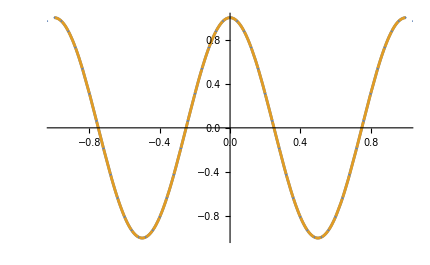

```mathematica
Show[Plot[{f[x], cft1[Sx][x]}, {x, -1, 1}], ListPlot[Transpose[{Range[r1, r2, T], Sx}]]]
```

```mathematica
f1[t_]:=Sx[[Round[t/T+1-(r1/T)]]]
Grid[Table[{n, f[n T],f1[n T]}, {n, -5, 5}]]
```

-5 | 0.309017 | 0.309017
-4 | 0.535827 | 0.535827
-3 | 0.728969 | 0.728969
-2 | 0.876307 | 0.876307
-1 | 0.968583 | 0.968583
0 | 1. | 1.
1 | 0.968583 | 0.968583
2 | 0.876307 | 0.876307
3 | 0.728969 | 0.728969
4 | 0.535827 | 0.535827
5 | 0.309017 | 0.309017

```mathematica
cft2[S_][t_]:=Sum[f[n T]*sincn[(t-n T)/T], {n, Floor[r1], Floor[r2]}]
```

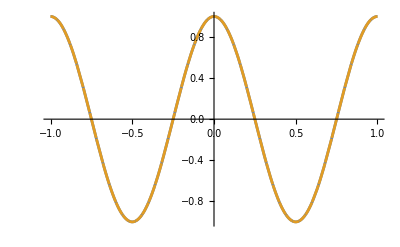

```mathematica
Plot[{f[x], cft2[Sx][x]}, {x, -1, 1}]
```

```mathematica
cft3[S_][t_]:=(Table[f[n T], {n, Floor[r1], Floor[r2]}]).Table[sincn[(t-n T)/T], {n, Floor[r1], Floor[r2]}]
```

```mathematica
Plot[{f[x], cft3[Sx][x]}, {x, -1, 1}]
```

-Graphics-